Q1 a)

```mathematica
<<Notation`
```

```mathematica
Symbolize[Subscript[x, t+Δt]]
```

Symbolize::bsymbexs: Warning: The box structure attempting to be symbolized has a similar or identical symbol already defined, possibly overriding previously symbolized box structure.

```mathematica
Symbolize[Subscript[ẋ, t+Δt]]
```

```mathematica
Symbolize[Subscript[x^(..), t+Δt]]
```

```mathematica
Symbolize[Subscript[x, t+γΔt]]
```

```mathematica
Symbolize[Subscript[ẋ, t+γΔt]]
```

```mathematica
Symbolize[Subscript[x^(..), t+γΔt]]
```

```mathematica
Symbolize[Subscript[x, t]]
```

```mathematica
Symbolize[Subscript[ẋ, t]]
```

```mathematica
Symbolize[Subscript[x^(..), t]]
```

```mathematica
Symbolize[Subscript[r, t+Δt]]
```

```mathematica
Symbolize[Subscript[r, t+γΔt]]
```

```mathematica
Symbolize[Subscript[Ω, o]]
```

```mathematica
Symbolize[Subscript[Ω̄, d]]
```

```mathematica
Symbolize[ξ̄]
```

```mathematica
Symbolize[Subscript[β, 1]]
```

```mathematica
Symbolize[Subscript[β, 2]]
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
ξ=0;
```

```mathematica
Column[Collect[{Subscript[x^(..), t+γΔt]+2ξ ω Subscript[ẋ, t+γΔt]+ω^2 Subscript[x, t+γΔt]==Subscript[r, t+γΔt] ,
Subscript[x, t+γΔt]==Subscript[x, t]+(γ Δt)/2(Subscript[ẋ, t]+Subscript[ẋ, t+γΔt]),
Subscript[ẋ, t+γΔt]==Subscript[ẋ, t]+(γ Δt)/2(Subscript[x^(..), t]+Subscript[x^(..), t+γΔt]),
Subscript[x^(..), t+Δt]+2ξ ω Subscript[ẋ, t+Δt]+ω^2 Subscript[x, t+Δt]==Subscript[r, t+Δt] ,
Subscript[x, t+Δt]==Subscript[x, t]+γ Δt((1-Subscript[β, 1])Subscript[ẋ, t]+Subscript[β, 1] Subscript[ẋ, t+γΔt])+(1-γ)Δt((1-Subscript[β, 2])Subscript[ẋ, t+γΔt]+Subscript[β, 2] Subscript[ẋ, t+Δt]),
Subscript[ẋ, t+Δt]==Subscript[ẋ, t]+γ Δt((1-Subscript[β, 1])Subscript[x^(..), t]+Subscript[β, 1] Subscript[x^(..), t+γΔt])+(1-γ)Δt((1-Subscript[β, 2])Subscript[x^(..), t+γΔt]+Subscript[β, 2] Subscript[x^(..), t+Δt])},{Subscript[x^(..), t+γΔt],Subscript[ẋ, t+γΔt],Subscript[x, t+γΔt],Subscript[x^(..), t+Δt],Subscript[ẋ, t+Δt],Subscript[x, t+Δt]}]]
```

(x^(..))_(t+γΔt)+2 (ẋ)_(t+γΔt) ξ ω+x_(t+γΔt) ω^2==r_(t+γΔt)
x_(t+γΔt)==x_t+1/2 (ẋ)_t γ Δt+1/2 (ẋ)_(t+γΔt) γ Δt
(ẋ)_(t+γΔt)==(ẋ)_t+1/2 (x^(..))_t γ Δt+1/2 (x^(..))_(t+γΔt) γ Δt
(x^(..))_(t+Δt)+2 (ẋ)_(t+Δt) ξ ω+x_(t+Δt) ω^2==r_(t+Δt)
x_(t+Δt)==x_t+(ẋ)_(t+Δt) β_2 (1-γ) Δt+(ẋ)_t (1-β_1) γ Δt+(ẋ)_(t+γΔt) ((1-β_2) (1-γ) Δt+β_1 γ Δt)
(ẋ)_(t+Δt)==(ẋ)_t+(x^(..))_(t+Δt) β_2 (1-γ) Δt+(x^(..))_t (1-β_1) γ Δt+(x^(..))_(t+γΔt) ((1-β_2) (1-γ) Δt+β_1 γ Δt)

```mathematica
Collect[Subscript[x, t+Δt]-Subscript[ẋ, t+Δt] Subscript[β, 2] (1-γ) Δt-Subscript[ẋ, t+γΔt] ((1-Subscript[β, 2]) (1-γ) Δt+Subscript[β, 1] γ Δt)==Subscript[x, t]+Subscript[ẋ, t] (1-Subscript[β, 1]) γ Δt,{Subscript[x^(..), t+γΔt],Subscript[ẋ, t+γΔt],Subscript[x, t+γΔt],Subscript[x^(..), t+Δt],Subscript[ẋ, t+Δt],Subscript[x, t+Δt]}]
```

x_(t+Δt)-(ẋ)_(t+Δt) β_2 (1-γ) Δt+(ẋ)_(t+γΔt) (-(1-β_2) (1-γ) Δt-β_1 γ Δt)==x_t+(ẋ)_t (1-β_1) γ Δt

```mathematica
Collect[Subscript[ẋ, t+Δt]-Subscript[x^(..), t+Δt] Subscript[β, 2] (1-γ) Δt-Subscript[x^(..), t+γΔt] ((1-Subscript[β, 2]) (1-γ) Δt+Subscript[β, 1] γ Δt)==Subscript[ẋ, t]+Subscript[x^(..), t] (1-Subscript[β, 1]) γ Δt,{Subscript[x^(..), t+γΔt],Subscript[ẋ, t+γΔt],Subscript[x, t+γΔt],Subscript[x^(..), t+Δt],Subscript[ẋ, t+Δt],Subscript[x, t+Δt]}]
```

(ẋ)_(t+Δt)-(x^(..))_(t+Δt) β_2 (1-γ) Δt+(x^(..))_(t+γΔt) (-(1-β_2) (1-γ) Δt-β_1 γ Δt)==(ẋ)_t+(x^(..))_t (1-β_1) γ Δt

```mathematica
Solve[
Subscript[x^(..), t+γΔt]+2ξ ω Subscript[ẋ, t+γΔt]+ω^2 Subscript[x, t+γΔt]==Subscript[r, t+γΔt] &&
Subscript[x, t+γΔt]==Subscript[x, t]+(γ Δt)/2(Subscript[ẋ, t]+Subscript[ẋ, t+γΔt])&&
Subscript[ẋ, t+γΔt]==Subscript[ẋ, t]+(γ Δt)/2(Subscript[x^(..), t]+Subscript[x^(..), t+γΔt]) &&
Subscript[x^(..), t+Δt]+2ξ ω Subscript[ẋ, t+Δt]+ω^2 Subscript[x, t+Δt]==Subscript[r, t+Δt] &&
Subscript[x, t+Δt]==Subscript[x, t]+γ Δt((1-Subscript[β, 1])Subscript[ẋ, t]+Subscript[β, 1] Subscript[ẋ, t+γΔt])+(1-γ)Δt((1-Subscript[β, 2])Subscript[ẋ, t+γΔt]+Subscript[β, 2] Subscript[ẋ, t+Δt])&&
Subscript[ẋ, t+Δt]==Subscript[ẋ, t]+γ Δt((1-Subscript[β, 1])Subscript[x^(..), t]+Subscript[β, 1] Subscript[x^(..), t+γΔt])+(1-γ)Δt((1-Subscript[β, 2])Subscript[x^(..), t+γΔt]+Subscript[β, 2] Subscript[x^(..), t+Δt]),
{Subscript[x^(..), t+γΔt],Subscript[ẋ, t+γΔt],Subscript[x, t+γΔt],Subscript[x^(..), t+Δt],Subscript[ẋ, t+Δt],Subscript[x, t+Δt]}]
```

{{(x^(..))_(t+γΔt)→-(-4 r_(t+γΔt)+4 x_t ω^2+4 (ẋ)_t γ Δt ω^2+(x^(..))_t γ^2 Δt^2 ω^2)/(4+γ^2 Δt^2 ω^2),(ẋ)_(t+γΔt)→-(-4 (ẋ)_t-2 r_(t+γΔt) γ Δt-2 (x^(..))_t γ Δt+2 x_t γ Δt ω^2+(ẋ)_t γ^2 Δt^2 ω^2)/(4+γ^2 Δt^2 ω^2),x_(t+γΔt)→-(-4 x_t-4 (ẋ)_t γ Δt-r_(t+γΔt) γ^2 Δt^2-(x^(..))_t γ^2 Δt^2)/(4+γ^2 Δt^2 ω^2),(x^(..))_(t+Δt)→-((-4 r_(t+Δt)+4 x_t ω^2+4 (ẋ)_t Δt ω^2+4 r_(t+γΔt) β_2 Δt^2 ω^2-4 r_(t+γΔt) β_2^2 Δt^2 ω^2+2 r_(t+γΔt) γ Δt^2 ω^2+2 (x^(..))_t γ Δt^2 ω^2-10 r_(t+γΔt) β_2 γ Δt^2 ω^2+2 (x^(..))_t β_2 γ Δt^2 ω^2+4 r_(t+γΔt) β_1 β_2 γ Δt^2 ω^2-4 (x^(..))_t β_1 β_2 γ Δt^2 ω^2+8 r_(t+γΔt) β_2^2 γ Δt^2 ω^2-2 r_(t+γΔt) γ^2 Δt^2 ω^2-r_(t+Δt) γ^2 Δt^2 ω^2-2 (x^(..))_t γ^2 Δt^2 ω^2+2 r_(t+γΔt) β_1 γ^2 Δt^2 ω^2+2 (x^(..))_t β_1 γ^2 Δt^2 ω^2+6 r_(t+γΔt) β_2 γ^2 Δt^2 ω^2-2 (x^(..))_t β_2 γ^2 Δt^2 ω^2-4 r_(t+γΔt) β_1 β_2 γ^2 Δt^2 ω^2+4 (x^(..))_t β_1 β_2 γ^2 Δt^2 ω^2-4 r_(t+γΔt) β_2^2 γ^2 Δt^2 ω^2-4 x_t β_2 Δt^2 ω^4+4 x_t β_2^2 Δt^2 ω^4-2 x_t γ Δt^2 ω^4+10 x_t β_2 γ Δt^2 ω^4-4 x_t β_1 β_2 γ Δt^2 ω^4-8 x_t β_2^2 γ Δt^2 ω^4+3 x_t γ^2 Δt^2 ω^4-2 x_t β_1 γ^2 Δt^2 ω^4-6 x_t β_2 γ^2 Δt^2 ω^4+4 x_t β_1 β_2 γ^2 Δt^2 ω^4+4 x_t β_2^2 γ^2 Δt^2 ω^4-4 (ẋ)_t β_2 γ Δt^3 ω^4+4 (ẋ)_t β_2^2 γ Δt^3 ω^4-(ẋ)_t γ^2 Δt^3 ω^4+10 (ẋ)_t β_2 γ^2 Δt^3 ω^4-4 (ẋ)_t β_1 β_2 γ^2 Δt^3 ω^4-8 (ẋ)_t β_2^2 γ^2 Δt^3 ω^4+2 (ẋ)_t γ^3 Δt^3 ω^4-2 (ẋ)_t β_1 γ^3 Δt^3 ω^4-6 (ẋ)_t β_2 γ^3 Δt^3 ω^4+4 (ẋ)_t β_1 β_2 γ^3 Δt^3 ω^4+4 (ẋ)_t β_2^2 γ^3 Δt^3 ω^4-(x^(..))_t β_2 γ^2 Δt^4 ω^4+(x^(..))_t β_2^2 γ^2 Δt^4 ω^4+3 (x^(..))_t β_2 γ^3 Δt^4 ω^4-2 (x^(..))_t β_1 β_2 γ^3 Δt^4 ω^4-2 (x^(..))_t β_2^2 γ^3 Δt^4 ω^4-2 (x^(..))_t β_2 γ^4 Δt^4 ω^4+2 (x^(..))_t β_1 β_2 γ^4 Δt^4 ω^4+(x^(..))_t β_2^2 γ^4 Δt^4 ω^4)/((4+γ^2 Δt^2 ω^2) (1+β_2^2 Δt^2 ω^2-2 β_2^2 γ Δt^2 ω^2+β_2^2 γ^2 Δt^2 ω^2))),(ẋ)_(t+Δt)→-((-4 (ẋ)_t-4 r_(t+γΔt) Δt+4 r_(t+γΔt) β_2 Δt-4 r_(t+Δt) β_2 Δt+4 r_(t+γΔt) γ Δt-4 (x^(..))_t γ Δt-4 r_(t+γΔt) β_1 γ Δt+4 (x^(..))_t β_1 γ Δt-4 r_(t+γΔt) β_2 γ Δt+4 r_(t+Δt) β_2 γ Δt+4 x_t Δt ω^2-4 x_t γ Δt ω^2+4 x_t β_1 γ Δt ω^2+4 (ẋ)_t β_2 Δt^2 ω^2-4 (ẋ)_t β_2^2 Δt^2 ω^2+4 (ẋ)_t γ Δt^2 ω^2-8 (ẋ)_t β_2 γ Δt^2 ω^2+8 (ẋ)_t β_2^2 γ Δt^2 ω^2-5 (ẋ)_t γ^2 Δt^2 ω^2+4 (ẋ)_t β_1 γ^2 Δt^2 ω^2+4 (ẋ)_t β_2 γ^2 Δt^2 ω^2-4 (ẋ)_t β_2^2 γ^2 Δt^2 ω^2+2 r_(t+γΔt) β_2 γ Δt^3 ω^2+2 (x^(..))_t β_2 γ Δt^3 ω^2-2 r_(t+γΔt) β_2^2 γ Δt^3 ω^2-2 (x^(..))_t β_2^2 γ Δt^3 ω^2+(x^(..))_t γ^2 Δt^3 ω^2-4 r_(t+γΔt) β_2 γ^2 Δt^3 ω^2-r_(t+Δt) β_2 γ^2 Δt^3 ω^2-5 (x^(..))_t β_2 γ^2 Δt^3 ω^2+2 r_(t+γΔt) β_1 β_2 γ^2 Δt^3 ω^2+2 (x^(..))_t β_1 β_2 γ^2 Δt^3 ω^2+4 r_(t+γΔt) β_2^2 γ^2 Δt^3 ω^2+4 (x^(..))_t β_2^2 γ^2 Δt^3 ω^2-2 (x^(..))_t γ^3 Δt^3 ω^2+2 (x^(..))_t β_1 γ^3 Δt^3 ω^2+2 r_(t+γΔt) β_2 γ^3 Δt^3 ω^2+r_(t+Δt) β_2 γ^3 Δt^3 ω^2+3 (x^(..))_t β_2 γ^3 Δt^3 ω^2-2 r_(t+γΔt) β_1 β_2 γ^3 Δt^3 ω^2-2 (x^(..))_t β_1 β_2 γ^3 Δt^3 ω^2-2 r_(t+γΔt) β_2^2 γ^3 Δt^3 ω^2-2 (x^(..))_t β_2^2 γ^3 Δt^3 ω^2-2 x_t β_2 γ Δt^3 ω^4+2 x_t β_2^2 γ Δt^3 ω^4+5 x_t β_2 γ^2 Δt^3 ω^4-2 x_t β_1 β_2 γ^2 Δt^3 ω^4-4 x_t β_2^2 γ^2 Δt^3 ω^4-3 x_t β_2 γ^3 Δt^3 ω^4+2 x_t β_1 β_2 γ^3 Δt^3 ω^4+2 x_t β_2^2 γ^3 Δt^3 ω^4-(ẋ)_t β_2 γ^2 Δt^4 ω^4+(ẋ)_t β_2^2 γ^2 Δt^4 ω^4+3 (ẋ)_t β_2 γ^3 Δt^4 ω^4-2 (ẋ)_t β_1 β_2 γ^3 Δt^4 ω^4-2 (ẋ)_t β_2^2 γ^3 Δt^4 ω^4-2 (ẋ)_t β_2 γ^4 Δt^4 ω^4+2 (ẋ)_t β_1 β_2 γ^4 Δt^4 ω^4+(ẋ)_t β_2^2 γ^4 Δt^4 ω^4)/((4+γ^2 Δt^2 ω^2) (1+β_2^2 Δt^2 ω^2-2 β_2^2 γ Δt^2 ω^2+β_2^2 γ^2 Δt^2 ω^2))),x_(t+Δt)→-((-4 x_t-4 (ẋ)_t Δt-4 r_(t+γΔt) β_2 Δt^2+4 r_(t+γΔt) β_2^2 Δt^2-4 r_(t+Δt) β_2^2 Δt^2-2 r_(t+γΔt) γ Δt^2-2 (x^(..))_t γ Δt^2+10 r_(t+γΔt) β_2 γ Δt^2-2 (x^(..))_t β_2 γ Δt^2-4 r_(t+γΔt) β_1 β_2 γ Δt^2+4 (x^(..))_t β_1 β_2 γ Δt^2-8 r_(t+γΔt) β_2^2 γ Δt^2+8 r_(t+Δt) β_2^2 γ Δt^2+2 r_(t+γΔt) γ^2 Δt^2+2 (x^(..))_t γ^2 Δt^2-2 r_(t+γΔt) β_1 γ^2 Δt^2-2 (x^(..))_t β_1 γ^2 Δt^2-6 r_(t+γΔt) β_2 γ^2 Δt^2+2 (x^(..))_t β_2 γ^2 Δt^2+4 r_(t+γΔt) β_1 β_2 γ^2 Δt^2-4 (x^(..))_t β_1 β_2 γ^2 Δt^2+4 r_(t+γΔt) β_2^2 γ^2 Δt^2-4 r_(t+Δt) β_2^2 γ^2 Δt^2+4 x_t β_2 Δt^2 ω^2-4 x_t β_2^2 Δt^2 ω^2+2 x_t γ Δt^2 ω^2-10 x_t β_2 γ Δt^2 ω^2+4 x_t β_1 β_2 γ Δt^2 ω^2+8 x_t β_2^2 γ Δt^2 ω^2-3 x_t γ^2 Δt^2 ω^2+2 x_t β_1 γ^2 Δt^2 ω^2+6 x_t β_2 γ^2 Δt^2 ω^2-4 x_t β_1 β_2 γ^2 Δt^2 ω^2-4 x_t β_2^2 γ^2 Δt^2 ω^2+4 (ẋ)_t β_2 γ Δt^3 ω^2-4 (ẋ)_t β_2^2 γ Δt^3 ω^2+(ẋ)_t γ^2 Δt^3 ω^2-10 (ẋ)_t β_2 γ^2 Δt^3 ω^2+4 (ẋ)_t β_1 β_2 γ^2 Δt^3 ω^2+8 (ẋ)_t β_2^2 γ^2 Δt^3 ω^2-2 (ẋ)_t γ^3 Δt^3 ω^2+2 (ẋ)_t β_1 γ^3 Δt^3 ω^2+6 (ẋ)_t β_2 γ^3 Δt^3 ω^2-4 (ẋ)_t β_1 β_2 γ^3 Δt^3 ω^2-4 (ẋ)_t β_2^2 γ^3 Δt^3 ω^2+(x^(..))_t β_2 γ^2 Δt^4 ω^2-r_(t+Δt) β_2^2 γ^2 Δt^4 ω^2-(x^(..))_t β_2^2 γ^2 Δt^4 ω^2-3 (x^(..))_t β_2 γ^3 Δt^4 ω^2+2 (x^(..))_t β_1 β_2 γ^3 Δt^4 ω^2+2 r_(t+Δt) β_2^2 γ^3 Δt^4 ω^2+2 (x^(..))_t β_2^2 γ^3 Δt^4 ω^2+2 (x^(..))_t β_2 γ^4 Δt^4 ω^2-2 (x^(..))_t β_1 β_2 γ^4 Δt^4 ω^2-r_(t+Δt) β_2^2 γ^4 Δt^4 ω^2-(x^(..))_t β_2^2 γ^4 Δt^4 ω^2)/((4+γ^2 Δt^2 ω^2) (1+β_2^2 Δt^2 ω^2-2 β_2^2 γ Δt^2 ω^2+β_2^2 γ^2 Δt^2 ω^2)))}}

```mathematica
ClearAll["Global`*"]
```

```mathematica
recursive=
{
Collect[Subscript[x^(..), t+Δt]-(-((-4 Subscript[r, t+Δt]+4 Subscript[x, t] ω^2+4 Subscript[ẋ, t] Δt ω^2+4 Subscript[r, t+γΔt] Subscript[β, 2] Δt^2 ω^2-4 Subscript[r, t+γΔt] Subscript[β, 2]^2 Δt^2 ω^2+2 Subscript[r, t+γΔt] γ Δt^2 ω^2+2 Subscript[x^(..), t] γ Δt^2 ω^2-10 Subscript[r, t+γΔt] Subscript[β, 2] γ Δt^2 ω^2+2 Subscript[x^(..), t] Subscript[β, 2] γ Δt^2 ω^2+4 Subscript[r, t+γΔt] Subscript[β, 1] Subscript[β, 2] γ Δt^2 ω^2-4 Subscript[x^(..), t] Subscript[β, 1] Subscript[β, 2] γ Δt^2 ω^2+8 Subscript[r, t+γΔt] Subscript[β, 2]^2 γ Δt^2 ω^2-2 Subscript[r, t+γΔt] γ^2 Δt^2 ω^2-Subscript[r, t+Δt] γ^2 Δt^2 ω^2-2 Subscript[x^(..), t] γ^2 Δt^2 ω^2+2 Subscript[r, t+γΔt] Subscript[β, 1] γ^2 Δt^2 ω^2+2 Subscript[x^(..), t] Subscript[β, 1] γ^2 Δt^2 ω^2+6 Subscript[r, t+γΔt] Subscript[β, 2] γ^2 Δt^2 ω^2-2 Subscript[x^(..), t] Subscript[β, 2] γ^2 Δt^2 ω^2-4 Subscript[r, t+γΔt] Subscript[β, 1] Subscript[β, 2] γ^2 Δt^2 ω^2+4 Subscript[x^(..), t] Subscript[β, 1] Subscript[β, 2] γ^2 Δt^2 ω^2-4 Subscript[r, t+γΔt] Subscript[β, 2]^2 γ^2 Δt^2 ω^2-4 Subscript[x, t] Subscript[β, 2] Δt^2 ω^4+4 Subscript[x, t] Subscript[β, 2]^2 Δt^2 ω^4-2 Subscript[x, t] γ Δt^2 ω^4+10 Subscript[x, t] Subscript[β, 2] γ Δt^2 ω^4-4 Subscript[x, t] Subscript[β, 1] Subscript[β, 2] γ Δt^2 ω^4-8 Subscript[x, t] Subscript[β, 2]^2 γ Δt^2 ω^4+3 Subscript[x, t] γ^2 Δt^2 ω^4-2 Subscript[x, t] Subscript[β, 1] γ^2 Δt^2 ω^4-6 Subscript[x, t] Subscript[β, 2] γ^2 Δt^2 ω^4+4 Subscript[x, t] Subscript[β, 1] Subscript[β, 2] γ^2 Δt^2 ω^4+4 Subscript[x, t] Subscript[β, 2]^2 γ^2 Δt^2 ω^4-4 Subscript[ẋ, t] Subscript[β, 2] γ Δt^3 ω^4+4 Subscript[ẋ, t] Subscript[β, 2]^2 γ Δt^3 ω^4-Subscript[ẋ, t] γ^2 Δt^3 ω^4+10 Subscript[ẋ, t] Subscript[β, 2] γ^2 Δt^3 ω^4-4 Subscript[ẋ, t] Subscript[β, 1] Subscript[β, 2] γ^2 Δt^3 ω^4-8 Subscript[ẋ, t] Subscript[β, 2]^2 γ^2 Δt^3 ω^4+2 Subscript[ẋ, t] γ^3 Δt^3 ω^4-2 Subscript[ẋ, t] Subscript[β, 1] γ^3 Δt^3 ω^4-6 Subscript[ẋ, t] Subscript[β, 2] γ^3 Δt^3 ω^4+4 Subscript[ẋ, t] Subscript[β, 1] Subscript[β, 2] γ^3 Δt^3 ω^4+4 Subscript[ẋ, t] Subscript[β, 2]^2 γ^3 Δt^3 ω^4-Subscript[x^(..), t] Subscript[β, 2] γ^2 Δt^4 ω^4+Subscript[x^(..), t] Subscript[β, 2]^2 γ^2 Δt^4 ω^4+3 Subscript[x^(..), t] Subscript[β, 2] γ^3 Δt^4 ω^4-2 Subscript[x^(..), t] Subscript[β, 1] Subscript[β, 2] γ^3 Δt^4 ω^4-2 Subscript[x^(..), t] Subscript[β, 2]^2 γ^3 Δt^4 ω^4-2 Subscript[x^(..), t] Subscript[β, 2] γ^4 Δt^4 ω^4+2 Subscript[x^(..), t] Subscript[β, 1] Subscript[β, 2] γ^4 Δt^4 ω^4+Subscript[x^(..), t] Subscript[β, 2]^2 γ^4 Δt^4 ω^4)/((4+γ^2 Δt^2 ω^2) (1+Subscript[β, 2]^2 Δt^2 ω^2-2 Subscript[β, 2]^2 γ Δt^2 ω^2+Subscript[β, 2]^2 γ^2 Δt^2 ω^2)))),{Subscript[x^(..), t],Subscript[ẋ, t],Subscript[x, t],Subscript[r, t+Δt],Subscript[r, t+γΔt]}],
Collect[Subscript[ẋ, t+Δt]-(-((-4 Subscript[ẋ, t]-4 Subscript[r, t+γΔt] Δt+4 Subscript[r, t+γΔt] Subscript[β, 2] Δt-4 Subscript[r, t+Δt] Subscript[β, 2] Δt+4 Subscript[r, t+γΔt] γ Δt-4 Subscript[x^(..), t] γ Δt-4 Subscript[r, t+γΔt] Subscript[β, 1] γ Δt+4 Subscript[x^(..), t] Subscript[β, 1] γ Δt-4 Subscript[r, t+γΔt] Subscript[β, 2] γ Δt+4 Subscript[r, t+Δt] Subscript[β, 2] γ Δt+4 Subscript[x, t] Δt ω^2-4 Subscript[x, t] γ Δt ω^2+4 Subscript[x, t] Subscript[β, 1] γ Δt ω^2+4 Subscript[ẋ, t] Subscript[β, 2] Δt^2 ω^2-4 Subscript[ẋ, t] Subscript[β, 2]^2 Δt^2 ω^2+4 Subscript[ẋ, t] γ Δt^2 ω^2-8 Subscript[ẋ, t] Subscript[β, 2] γ Δt^2 ω^2+8 Subscript[ẋ, t] Subscript[β, 2]^2 γ Δt^2 ω^2-5 Subscript[ẋ, t] γ^2 Δt^2 ω^2+4 Subscript[ẋ, t] Subscript[β, 1] γ^2 Δt^2 ω^2+4 Subscript[ẋ, t] Subscript[β, 2] γ^2 Δt^2 ω^2-4 Subscript[ẋ, t] Subscript[β, 2]^2 γ^2 Δt^2 ω^2+2 Subscript[r, t+γΔt] Subscript[β, 2] γ Δt^3 ω^2+2 Subscript[x^(..), t] Subscript[β, 2] γ Δt^3 ω^2-2 Subscript[r, t+γΔt] Subscript[β, 2]^2 γ Δt^3 ω^2-2 Subscript[x^(..), t] Subscript[β, 2]^2 γ Δt^3 ω^2+Subscript[x^(..), t] γ^2 Δt^3 ω^2-4 Subscript[r, t+γΔt] Subscript[β, 2] γ^2 Δt^3 ω^2-Subscript[r, t+Δt] Subscript[β, 2] γ^2 Δt^3 ω^2-5 Subscript[x^(..), t] Subscript[β, 2] γ^2 Δt^3 ω^2+2 Subscript[r, t+γΔt] Subscript[β, 1] Subscript[β, 2] γ^2 Δt^3 ω^2+2 Subscript[x^(..), t] Subscript[β, 1] Subscript[β, 2] γ^2 Δt^3 ω^2+4 Subscript[r, t+γΔt] Subscript[β, 2]^2 γ^2 Δt^3 ω^2+4 Subscript[x^(..), t] Subscript[β, 2]^2 γ^2 Δt^3 ω^2-2 Subscript[x^(..), t] γ^3 Δt^3 ω^2+2 Subscript[x^(..), t] Subscript[β, 1] γ^3 Δt^3 ω^2+2 Subscript[r, t+γΔt] Subscript[β, 2] γ^3 Δt^3 ω^2+Subscript[r, t+Δt] Subscript[β, 2] γ^3 Δt^3 ω^2+3 Subscript[x^(..), t] Subscript[β, 2] γ^3 Δt^3 ω^2-2 Subscript[r, t+γΔt] Subscript[β, 1] Subscript[β, 2] γ^3 Δt^3 ω^2-2 Subscript[x^(..), t] Subscript[β, 1] Subscript[β, 2] γ^3 Δt^3 ω^2-2 Subscript[r, t+γΔt] Subscript[β, 2]^2 γ^3 Δt^3 ω^2-2 Subscript[x^(..), t] Subscript[β, 2]^2 γ^3 Δt^3 ω^2-2 Subscript[x, t] Subscript[β, 2] γ Δt^3 ω^4+2 Subscript[x, t] Subscript[β, 2]^2 γ Δt^3 ω^4+5 Subscript[x, t] Subscript[β, 2] γ^2 Δt^3 ω^4-2 Subscript[x, t] Subscript[β, 1] Subscript[β, 2] γ^2 Δt^3 ω^4-4 Subscript[x, t] Subscript[β, 2]^2 γ^2 Δt^3 ω^4-3 Subscript[x, t] Subscript[β, 2] γ^3 Δt^3 ω^4+2 Subscript[x, t] Subscript[β, 1] Subscript[β, 2] γ^3 Δt^3 ω^4+2 Subscript[x, t] Subscript[β, 2]^2 γ^3 Δt^3 ω^4-Subscript[ẋ, t] Subscript[β, 2] γ^2 Δt^4 ω^4+Subscript[ẋ, t] Subscript[β, 2]^2 γ^2 Δt^4 ω^4+3 Subscript[ẋ, t] Subscript[β, 2] γ^3 Δt^4 ω^4-2 Subscript[ẋ, t] Subscript[β, 1] Subscript[β, 2] γ^3 Δt^4 ω^4-2 Subscript[ẋ, t] Subscript[β, 2]^2 γ^3 Δt^4 ω^4-2 Subscript[ẋ, t] Subscript[β, 2] γ^4 Δt^4 ω^4+2 Subscript[ẋ, t] Subscript[β, 1] Subscript[β, 2] γ^4 Δt^4 ω^4+Subscript[ẋ, t] Subscript[β, 2]^2 γ^4 Δt^4 ω^4)/((4+γ^2 Δt^2 ω^2) (1+Subscript[β, 2]^2 Δt^2 ω^2-2 Subscript[β, 2]^2 γ Δt^2 ω^2+Subscript[β, 2]^2 γ^2 Δt^2 ω^2))))//Factor,{Subscript[x^(..), t],Subscript[ẋ, t],Subscript[x, t],Subscript[r, t+Δt],Subscript[r, t+γΔt]}],
Collect[Subscript[x, t+Δt]-(-((-4 Subscript[x, t]-4 Subscript[ẋ, t] Δt-4 Subscript[r, t+γΔt] Subscript[β, 2] Δt^2+4 Subscript[r, t+γΔt] Subscript[β, 2]^2 Δt^2-4 Subscript[r, t+Δt] Subscript[β, 2]^2 Δt^2-2 Subscript[r, t+γΔt] γ Δt^2-2 Subscript[x^(..), t] γ Δt^2+10 Subscript[r, t+γΔt] Subscript[β, 2] γ Δt^2-2 Subscript[x^(..), t] Subscript[β, 2] γ Δt^2-4 Subscript[r, t+γΔt] Subscript[β, 1] Subscript[β, 2] γ Δt^2+4 Subscript[x^(..), t] Subscript[β, 1] Subscript[β, 2] γ Δt^2-8 Subscript[r, t+γΔt] Subscript[β, 2]^2 γ Δt^2+8 Subscript[r, t+Δt] Subscript[β, 2]^2 γ Δt^2+2 Subscript[r, t+γΔt] γ^2 Δt^2+2 Subscript[x^(..), t] γ^2 Δt^2-2 Subscript[r, t+γΔt] Subscript[β, 1] γ^2 Δt^2-2 Subscript[x^(..), t] Subscript[β, 1] γ^2 Δt^2-6 Subscript[r, t+γΔt] Subscript[β, 2] γ^2 Δt^2+2 Subscript[x^(..), t] Subscript[β, 2] γ^2 Δt^2+4 Subscript[r, t+γΔt] Subscript[β, 1] Subscript[β, 2] γ^2 Δt^2-4 Subscript[x^(..), t] Subscript[β, 1] Subscript[β, 2] γ^2 Δt^2+4 Subscript[r, t+γΔt] Subscript[β, 2]^2 γ^2 Δt^2-4 Subscript[r, t+Δt] Subscript[β, 2]^2 γ^2 Δt^2+4 Subscript[x, t] Subscript[β, 2] Δt^2 ω^2-4 Subscript[x, t] Subscript[β, 2]^2 Δt^2 ω^2+2 Subscript[x, t] γ Δt^2 ω^2-10 Subscript[x, t] Subscript[β, 2] γ Δt^2 ω^2+4 Subscript[x, t] Subscript[β, 1] Subscript[β, 2] γ Δt^2 ω^2+8 Subscript[x, t] Subscript[β, 2]^2 γ Δt^2 ω^2-3 Subscript[x, t] γ^2 Δt^2 ω^2+2 Subscript[x, t] Subscript[β, 1] γ^2 Δt^2 ω^2+6 Subscript[x, t] Subscript[β, 2] γ^2 Δt^2 ω^2-4 Subscript[x, t] Subscript[β, 1] Subscript[β, 2] γ^2 Δt^2 ω^2-4 Subscript[x, t] Subscript[β, 2]^2 γ^2 Δt^2 ω^2+4 Subscript[ẋ, t] Subscript[β, 2] γ Δt^3 ω^2-4 Subscript[ẋ, t] Subscript[β, 2]^2 γ Δt^3 ω^2+Subscript[ẋ, t] γ^2 Δt^3 ω^2-10 Subscript[ẋ, t] Subscript[β, 2] γ^2 Δt^3 ω^2+4 Subscript[ẋ, t] Subscript[β, 1] Subscript[β, 2] γ^2 Δt^3 ω^2+8 Subscript[ẋ, t] Subscript[β, 2]^2 γ^2 Δt^3 ω^2-2 Subscript[ẋ, t] γ^3 Δt^3 ω^2+2 Subscript[ẋ, t] Subscript[β, 1] γ^3 Δt^3 ω^2+6 Subscript[ẋ, t] Subscript[β, 2] γ^3 Δt^3 ω^2-4 Subscript[ẋ, t] Subscript[β, 1] Subscript[β, 2] γ^3 Δt^3 ω^2-4 Subscript[ẋ, t] Subscript[β, 2]^2 γ^3 Δt^3 ω^2+Subscript[x^(..), t] Subscript[β, 2] γ^2 Δt^4 ω^2-Subscript[r, t+Δt] Subscript[β, 2]^2 γ^2 Δt^4 ω^2-Subscript[x^(..), t] Subscript[β, 2]^2 γ^2 Δt^4 ω^2-3 Subscript[x^(..), t] Subscript[β, 2] γ^3 Δt^4 ω^2+2 Subscript[x^(..), t] Subscript[β, 1] Subscript[β, 2] γ^3 Δt^4 ω^2+2 Subscript[r, t+Δt] Subscript[β, 2]^2 γ^3 Δt^4 ω^2+2 Subscript[x^(..), t] Subscript[β, 2]^2 γ^3 Δt^4 ω^2+2 Subscript[x^(..), t] Subscript[β, 2] γ^4 Δt^4 ω^2-2 Subscript[x^(..), t] Subscript[β, 1] Subscript[β, 2] γ^4 Δt^4 ω^2-Subscript[r, t+Δt] Subscript[β, 2]^2 γ^4 Δt^4 ω^2-Subscript[x^(..), t] Subscript[β, 2]^2 γ^4 Δt^4 ω^2)/((4+γ^2 Δt^2 ω^2) (1+Subscript[β, 2]^2 Δt^2 ω^2-2 Subscript[β, 2]^2 γ Δt^2 ω^2+Subscript[β, 2]^2 γ^2 Δt^2 ω^2))))//Factor,{Subscript[x^(..), t],Subscript[ẋ, t],Subscript[x, t],Subscript[r, t+γΔt],Subscript[r, t+Δt]}]
}/.{-1-Subscript[β, 2]^2 (1-γ)^2 Δt^2 ω^2->Subscript[η, 1]  , 4+γ^2 Δt^2 ω^2->Subscript[η, 2], 1+Subscript[β, 2]^2 Δt^2 ω^2-2 Subscript[β, 2]^2 γ Δt^2 ω^2+Subscript[β, 2]^2 γ^2 Δt^2 ω^2->Subscript[η, 3]}
```

{(x^(..))_(t+Δt)+r_(t+Δt) (-4/(η_2 η_3)-(γ^2 Δt^2 ω^2)/(η_2 η_3))+r_(t+γΔt) ((4 β_2 Δt^2 ω^2)/(η_2 η_3)-(4 β_2^2 Δt^2 ω^2)/(η_2 η_3)+(2 γ Δt^2 ω^2)/(η_2 η_3)-(10 β_2 γ Δt^2 ω^2)/(η_2 η_3)+(4 β_1 β_2 γ Δt^2 ω^2)/(η_2 η_3)+(8 β_2^2 γ Δt^2 ω^2)/(η_2 η_3)-(2 γ^2 Δt^2 ω^2)/(η_2 η_3)+(2 β_1 γ^2 Δt^2 ω^2)/(η_2 η_3)+(6 β_2 γ^2 Δt^2 ω^2)/(η_2 η_3)-(4 β_1 β_2 γ^2 Δt^2 ω^2)/(η_2 η_3)-(4 β_2^2 γ^2 Δt^2 ω^2)/(η_2 η_3))+x_t ((4 ω^2)/(η_2 η_3)-(4 β_2 Δt^2 ω^4)/(η_2 η_3)+(4 β_2^2 Δt^2 ω^4)/(η_2 η_3)-(2 γ Δt^2 ω^4)/(η_2 η_3)+(10 β_2 γ Δt^2 ω^4)/(η_2 η_3)-(4 β_1 β_2 γ Δt^2 ω^4)/(η_2 η_3)-(8 β_2^2 γ Δt^2 ω^4)/(η_2 η_3)+(3 γ^2 Δt^2 ω^4)/(η_2 η_3)-(2 β_1 γ^2 Δt^2 ω^4)/(η_2 η_3)-(6 β_2 γ^2 Δt^2 ω^4)/(η_2 η_3)+(4 β_1 β_2 γ^2 Δt^2 ω^4)/(η_2 η_3)+(4 β_2^2 γ^2 Δt^2 ω^4)/(η_2 η_3))+(ẋ)_t ((4 Δt ω^2)/(η_2 η_3)-(4 β_2 γ Δt^3 ω^4)/(η_2 η_3)+(4 β_2^2 γ Δt^3 ω^4)/(η_2 η_3)-(γ^2 Δt^3 ω^4)/(η_2 η_3)+(10 β_2 γ^2 Δt^3 ω^4)/(η_2 η_3)-(4 β_1 β_2 γ^2 Δt^3 ω^4)/(η_2 η_3)-(8 β_2^2 γ^2 Δt^3 ω^4)/(η_2 η_3)+(2 γ^3 Δt^3 ω^4)/(η_2 η_3)-(2 β_1 γ^3 Δt^3 ω^4)/(η_2 η_3)-(6 β_2 γ^3 Δt^3 ω^4)/(η_2 η_3)+(4 β_1 β_2 γ^3 Δt^3 ω^4)/(η_2 η_3)+(4 β_2^2 γ^3 Δt^3 ω^4)/(η_2 η_3))+(x^(..))_t ((2 γ Δt^2 ω^2)/(η_2 η_3)+(2 β_2 γ Δt^2 ω^2)/(η_2 η_3)-(4 β_1 β_2 γ Δt^2 ω^2)/(η_2 η_3)-(2 γ^2 Δt^2 ω^2)/(η_2 η_3)+(2 β_1 γ^2 Δt^2 ω^2)/(η_2 η_3)-(2 β_2 γ^2 Δt^2 ω^2)/(η_2 η_3)+(4 β_1 β_2 γ^2 Δt^2 ω^2)/(η_2 η_3)-(β_2 γ^2 Δt^4 ω^4)/(η_2 η_3)+(β_2^2 γ^2 Δt^4 ω^4)/(η_2 η_3)+(3 β_2 γ^3 Δt^4 ω^4)/(η_2 η_3)-(2 β_1 β_2 γ^3 Δt^4 ω^4)/(η_2 η_3)-(2 β_2^2 γ^3 Δt^4 ω^4)/(η_2 η_3)-(2 β_2 γ^4 Δt^4 ω^4)/(η_2 η_3)+(2 β_1 β_2 γ^4 Δt^4 ω^4)/(η_2 η_3)+(β_2^2 γ^4 Δt^4 ω^4)/(η_2 η_3)),(r_(t+Δt) (-4 β_2 Δt+4 β_2 γ Δt-β_2 γ^2 Δt^3 ω^2+β_2 γ^3 Δt^3 ω^2))/(η_2 η_3)+1/(η_2 η_3)r_(t+γΔt) (-4 Δt+4 β_2 Δt+4 γ Δt-4 β_1 γ Δt-4 β_2 γ Δt+2 β_2 γ Δt^3 ω^2-2 β_2^2 γ Δt^3 ω^2-4 β_2 γ^2 Δt^3 ω^2+2 β_1 β_2 γ^2 Δt^3 ω^2+4 β_2^2 γ^2 Δt^3 ω^2+2 β_2 γ^3 Δt^3 ω^2-2 β_1 β_2 γ^3 Δt^3 ω^2-2 β_2^2 γ^3 Δt^3 ω^2)+1/(η_2 η_3)(x^(..))_t (-4 γ Δt+4 β_1 γ Δt+2 β_2 γ Δt^3 ω^2-2 β_2^2 γ Δt^3 ω^2+γ^2 Δt^3 ω^2-5 β_2 γ^2 Δt^3 ω^2+2 β_1 β_2 γ^2 Δt^3 ω^2+4 β_2^2 γ^2 Δt^3 ω^2-2 γ^3 Δt^3 ω^2+2 β_1 γ^3 Δt^3 ω^2+3 β_2 γ^3 Δt^3 ω^2-2 β_1 β_2 γ^3 Δt^3 ω^2-2 β_2^2 γ^3 Δt^3 ω^2)+1/(η_2 η_3)x_t (4 Δt ω^2-4 γ Δt ω^2+4 β_1 γ Δt ω^2-2 β_2 γ Δt^3 ω^4+2 β_2^2 γ Δt^3 ω^4+5 β_2 γ^2 Δt^3 ω^4-2 β_1 β_2 γ^2 Δt^3 ω^4-4 β_2^2 γ^2 Δt^3 ω^4-3 β_2 γ^3 Δt^3 ω^4+2 β_1 β_2 γ^3 Δt^3 ω^4+2 β_2^2 γ^3 Δt^3 ω^4)+1/(η_2 η_3)(ẋ)_t (-4+4 β_2 Δt^2 ω^2-4 β_2^2 Δt^2 ω^2+4 γ Δt^2 ω^2-8 β_2 γ Δt^2 ω^2+8 β_2^2 γ Δt^2 ω^2-5 γ^2 Δt^2 ω^2+4 β_1 γ^2 Δt^2 ω^2+4 β_2 γ^2 Δt^2 ω^2-4 β_2^2 γ^2 Δt^2 ω^2-β_2 γ^2 Δt^4 ω^4+β_2^2 γ^2 Δt^4 ω^4+3 β_2 γ^3 Δt^4 ω^4-2 β_1 β_2 γ^3 Δt^4 ω^4-2 β_2^2 γ^3 Δt^4 ω^4-2 β_2 γ^4 Δt^4 ω^4+2 β_1 β_2 γ^4 Δt^4 ω^4+β_2^2 γ^4 Δt^4 ω^4)+(4 (ẋ)_(t+Δt)+4 (ẋ)_(t+Δt) β_2^2 Δt^2 ω^2-8 (ẋ)_(t+Δt) β_2^2 γ Δt^2 ω^2+(ẋ)_(t+Δt) γ^2 Δt^2 ω^2+4 (ẋ)_(t+Δt) β_2^2 γ^2 Δt^2 ω^2+(ẋ)_(t+Δt) β_2^2 γ^2 Δt^4 ω^4-2 (ẋ)_(t+Δt) β_2^2 γ^3 Δt^4 ω^4+(ẋ)_(t+Δt) β_2^2 γ^4 Δt^4 ω^4)/(η_2 η_3),(r_(t+γΔt) (-4 β_2 Δt^2+4 β_2^2 Δt^2-2 γ Δt^2+10 β_2 γ Δt^2-4 β_1 β_2 γ Δt^2-8 β_2^2 γ Δt^2+2 γ^2 Δt^2-2 β_1 γ^2 Δt^2-6 β_2 γ^2 Δt^2+4 β_1 β_2 γ^2 Δt^2+4 β_2^2 γ^2 Δt^2))/(η_2 η_3)+1/(η_2 η_3)x_t (-4+4 β_2 Δt^2 ω^2-4 β_2^2 Δt^2 ω^2+2 γ Δt^2 ω^2-10 β_2 γ Δt^2 ω^2+4 β_1 β_2 γ Δt^2 ω^2+8 β_2^2 γ Δt^2 ω^2-3 γ^2 Δt^2 ω^2+2 β_1 γ^2 Δt^2 ω^2+6 β_2 γ^2 Δt^2 ω^2-4 β_1 β_2 γ^2 Δt^2 ω^2-4 β_2^2 γ^2 Δt^2 ω^2)+1/(η_2 η_3)(ẋ)_t (-4 Δt+4 β_2 γ Δt^3 ω^2-4 β_2^2 γ Δt^3 ω^2+γ^2 Δt^3 ω^2-10 β_2 γ^2 Δt^3 ω^2+4 β_1 β_2 γ^2 Δt^3 ω^2+8 β_2^2 γ^2 Δt^3 ω^2-2 γ^3 Δt^3 ω^2+2 β_1 γ^3 Δt^3 ω^2+6 β_2 γ^3 Δt^3 ω^2-4 β_1 β_2 γ^3 Δt^3 ω^2-4 β_2^2 γ^3 Δt^3 ω^2)+(r_(t+Δt) (-4 β_2^2 Δt^2+8 β_2^2 γ Δt^2-4 β_2^2 γ^2 Δt^2-β_2^2 γ^2 Δt^4 ω^2+2 β_2^2 γ^3 Δt^4 ω^2-β_2^2 γ^4 Δt^4 ω^2))/(η_2 η_3)+1/(η_2 η_3)(x^(..))_t (-2 γ Δt^2-2 β_2 γ Δt^2+4 β_1 β_2 γ Δt^2+2 γ^2 Δt^2-2 β_1 γ^2 Δt^2+2 β_2 γ^2 Δt^2-4 β_1 β_2 γ^2 Δt^2+β_2 γ^2 Δt^4 ω^2-β_2^2 γ^2 Δt^4 ω^2-3 β_2 γ^3 Δt^4 ω^2+2 β_1 β_2 γ^3 Δt^4 ω^2+2 β_2^2 γ^3 Δt^4 ω^2+2 β_2 γ^4 Δt^4 ω^2-2 β_1 β_2 γ^4 Δt^4 ω^2-β_2^2 γ^4 Δt^4 ω^2)+(4 x_(t+Δt)+4 x_(t+Δt) β_2^2 Δt^2 ω^2-8 x_(t+Δt) β_2^2 γ Δt^2 ω^2+x_(t+Δt) γ^2 Δt^2 ω^2+4 x_(t+Δt) β_2^2 γ^2 Δt^2 ω^2+x_(t+Δt) β_2^2 γ^2 Δt^4 ω^4-2 x_(t+Δt) β_2^2 γ^3 Δt^4 ω^4+x_(t+Δt) β_2^2 γ^4 Δt^4 ω^4)/(η_2 η_3)}

```mathematica
a=-({{Coefficient[Part[recursive,1],Subscript[x^(..), t]], Coefficient[Part[recursive,1],Subscript[ẋ, t]], Coefficient[Part[recursive,1],Subscript[x, t]]}, {Coefficient[Part[recursive,2],Subscript[x^(..), t]], Coefficient[Part[recursive,2],Subscript[ẋ, t]], Coefficient[Part[recursive,2],Subscript[x, t]]}, {Coefficient[Part[recursive,3],Subscript[x^(..), t]], Coefficient[Part[recursive,3],Subscript[ẋ, t]], Coefficient[Part[recursive,3],Subscript[x, t]]}});
```

```mathematica
a//MatrixForm//Simplify
```

(-(γ Δt^2 ω^2 (2+2 (-1+β_1) γ+β_2^2 (-1+γ)^2 γ Δt^2 ω^2+β_2 (-1+γ) (-2+γ Δt^2 ω^2-2 γ^2 Δt^2 ω^2+2 β_1 (2+γ^2 Δt^2 ω^2))))/(η_2 η_3) | (-4 Δt ω^2+γ (-4 β_2^2 (-1+γ)^2+γ (1+2 (-1+β_1) γ)-2 β_2 (-1+γ) (2+(-3+2 β_1) γ)) Δt^3 ω^4)/(η_2 η_3) | (-4 ω^2+(-4 β_2^2 (-1+γ)^2-2 β_2 (-1+γ) (2+(-3+2 β_1) γ)+γ (2+(-3+2 β_1) γ)) Δt^2 ω^4)/(η_2 η_3)
(γ Δt (4+2 β_2^2 (-1+γ)^2 Δt^2 ω^2-γ Δt^2 ω^2+2 γ^2 Δt^2 ω^2+β_2 (-2+5 γ-3 γ^2) Δt^2 ω^2+2 β_1 (-2+β_2 (-1+γ) γ Δt^2 ω^2-γ^2 Δt^2 ω^2)))/(η_2 η_3) | (4-4 γ Δt^2 ω^2+(5-4 β_1) γ^2 Δt^2 ω^2-β_2^2 (-1+γ)^2 Δt^2 ω^2 (-4+γ^2 Δt^2 ω^2)-β_2 (-1+γ) Δt^2 ω^2 (-4+4 γ+γ^2 Δt^2 ω^2+2 (-1+β_1) γ^3 Δt^2 ω^2))/(η_2 η_3) | (Δt ω^2 (-4+β_2 (-5+2 β_1+4 β_2) γ^2 Δt^2 ω^2+(3-2 β_1-2 β_2) β_2 γ^3 Δt^2 ω^2+γ (4-4 β_1+2 β_2 Δt^2 ω^2-2 β_2^2 Δt^2 ω^2)))/(η_2 η_3)
(γ Δt^2 (2+2 (-1+β_1) γ+β_2^2 (-1+γ)^2 γ Δt^2 ω^2+β_2 (-1+γ) (-2+γ Δt^2 ω^2-2 γ^2 Δt^2 ω^2+2 β_1 (2+γ^2 Δt^2 ω^2))))/(η_2 η_3) | (Δt (4+4 β_2^2 (-1+γ)^2 γ Δt^2 ω^2-γ^2 Δt^2 ω^2-2 (-1+β_1) γ^3 Δt^2 ω^2+2 β_2 (-1+γ) γ (2+(-3+2 β_1) γ) Δt^2 ω^2))/(η_2 η_3) | (4+4 β_2^2 (-1+γ)^2 Δt^2 ω^2-2 γ Δt^2 ω^2+(3-2 β_1) γ^2 Δt^2 ω^2+2 β_2 (-1+γ) (2+(-3+2 β_1) γ) Δt^2 ω^2)/(η_2 η_3))

```mathematica
la=-({{Coefficient[Part[recursive,1],Subscript[r, t+γΔt]]}, {Coefficient[Part[recursive,2],Subscript[r, t+γΔt]]}, {Coefficient[Part[recursive,3],Subscript[r, t+γΔt]]}});
```

```mathematica
la//MatrixForm//Simplify
```

((2 (2 β_2 (-1+γ)-γ) (1+β_2 (-1+γ)+(-1+β_1) γ) Δt^2 ω^2)/((1+β_2^2 (-1+γ)^2 Δt^2 ω^2) (4+γ^2 Δt^2 ω^2))
(2 (1+β_2 (-1+γ)+(-1+β_1) γ) Δt (2+β_2 (-1+γ) γ Δt^2 ω^2))/((1+β_2^2 (-1+γ)^2 Δt^2 ω^2) (4+γ^2 Δt^2 ω^2))
-(2 (2 β_2 (-1+γ)-γ) (1+β_2 (-1+γ)+(-1+β_1) γ) Δt^2)/((1+β_2^2 (-1+γ)^2 Δt^2 ω^2) (4+γ^2 Δt^2 ω^2)))

```mathematica
lb=-({{Coefficient[Part[recursive,1],Subscript[r, t+Δt]]}, {Coefficient[Part[recursive,2],Subscript[r, t+Δt]]}, {Coefficient[Part[recursive,3],Subscript[r, t+Δt]]}});
```

```mathematica
lb//MatrixForm//Simplify
```

(1/(1+β_2^2 (-1+γ)^2 Δt^2 ω^2)
-(β_2 (-1+γ) Δt)/(1+β_2^2 (-1+γ)^2 Δt^2 ω^2)
(β_2^2 (-1+γ)^2 Δt^2)/(1+β_2^2 (-1+γ)^2 Δt^2 ω^2))

```mathematica
eigA=Eigenvalues[a];
```

```mathematica
eigA//MatrixForm//Simplify
```

(0
-(-4+4 β_2 Δt^2 ω^2-4 β_2^2 Δt^2 ω^2+4 γ Δt^2 ω^2-8 β_2 γ Δt^2 ω^2+8 β_2^2 γ Δt^2 ω^2-5 γ^2 Δt^2 ω^2+4 β_1 γ^2 Δt^2 ω^2+4 β_2 γ^2 Δt^2 ω^2-4 β_2^2 γ^2 Δt^2 ω^2-β_2 γ^2 Δt^4 ω^4+β_2^2 γ^2 Δt^4 ω^4+3 β_2 γ^3 Δt^4 ω^4-2 β_1 β_2 γ^3 Δt^4 ω^4-2 β_2^2 γ^3 Δt^4 ω^4-2 β_2 γ^4 Δt^4 ω^4+2 β_1 β_2 γ^4 Δt^4 ω^4+β_2^2 γ^4 Δt^4 ω^4+√(-Δt^2 ω^2 (4+4 β_2^2 (-1+γ)^2 γ Δt^2 ω^2-γ^2 Δt^2 ω^2-2 (-1+β_1) γ^3 Δt^2 ω^2+2 β_2 (-1+γ) γ (2+(-3+2 β_1) γ) Δt^2 ω^2)^2))/(η_2 η_3)
(4-4 β_2 Δt^2 ω^2+4 β_2^2 Δt^2 ω^2-4 γ Δt^2 ω^2+8 β_2 γ Δt^2 ω^2-8 β_2^2 γ Δt^2 ω^2+5 γ^2 Δt^2 ω^2-4 β_1 γ^2 Δt^2 ω^2-4 β_2 γ^2 Δt^2 ω^2+4 β_2^2 γ^2 Δt^2 ω^2+β_2 γ^2 Δt^4 ω^4-β_2^2 γ^2 Δt^4 ω^4-3 β_2 γ^3 Δt^4 ω^4+2 β_1 β_2 γ^3 Δt^4 ω^4+2 β_2^2 γ^3 Δt^4 ω^4+2 β_2 γ^4 Δt^4 ω^4-2 β_1 β_2 γ^4 Δt^4 ω^4-β_2^2 γ^4 Δt^4 ω^4+√(-Δt^2 ω^2 (4+4 β_2^2 (-1+γ)^2 γ Δt^2 ω^2-γ^2 Δt^2 ω^2-2 (-1+β_1) γ^3 Δt^2 ω^2+2 β_2 (-1+γ) γ (2+(-3+2 β_1) γ) Δt^2 ω^2)^2))/(η_2 η_3))

```mathematica
ξ=0;
```

```mathematica
ω=2 Pi/T;
```

```mathematica
λ1=Part[eigA,2]/.T->1//Simplify//Apart
```

-(1-β_2-2 γ+2 β_1 γ+β_2 γ)/(β_2 (-1+γ))+(4 (1-β_2-γ+β_1 γ+β_2 γ))/((-2 β_2+γ+2 β_2 γ) (1+p^2 π^2 γ^2))+(2 β_2+γ-4 β_2 γ-2 γ^2+2 β_1 γ^2+2 β_2 γ^2)/(β_2 (-1+γ) (-2 β_2+γ+2 β_2 γ) (1+4 p^2 π^2 β_2^2-8 p^2 π^2 β_2^2 γ+4 p^2 π^2 β_2^2 γ^2))+(2 π γ^2 √(-(p+p^3 π^2 γ (4 β_2^2 (-1+γ)^2+γ (-1-2 (-1+β_1) γ)+2 β_2 (-1+γ) (2+(-3+2 β_1) γ)))^2))/((1+p^2 π^2 γ^2) (4 β_2^2-8 β_2^2 γ-γ^2+4 β_2^2 γ^2))-(8 π β_2^2 √(-(p+p^3 π^2 γ (4 β_2^2 (-1+γ)^2+γ (-1-2 (-1+β_1) γ)+2 β_2 (-1+γ) (2+(-3+2 β_1) γ)))^2))/((4 β_2^2-8 β_2^2 γ-γ^2+4 β_2^2 γ^2) (1+4 p^2 π^2 β_2^2-8 p^2 π^2 β_2^2 γ+4 p^2 π^2 β_2^2 γ^2))+(16 π β_2^2 γ √(-(p+p^3 π^2 γ (4 β_2^2 (-1+γ)^2+γ (-1-2 (-1+β_1) γ)+2 β_2 (-1+γ) (2+(-3+2 β_1) γ)))^2))/((4 β_2^2-8 β_2^2 γ-γ^2+4 β_2^2 γ^2) (1+4 p^2 π^2 β_2^2-8 p^2 π^2 β_2^2 γ+4 p^2 π^2 β_2^2 γ^2))-(8 π β_2^2 γ^2 √(-(p+p^3 π^2 γ (4 β_2^2 (-1+γ)^2+γ (-1-2 (-1+β_1) γ)+2 β_2 (-1+γ) (2+(-3+2 β_1) γ)))^2))/((4 β_2^2-8 β_2^2 γ-γ^2+4 β_2^2 γ^2) (1+4 p^2 π^2 β_2^2-8 p^2 π^2 β_2^2 γ+4 p^2 π^2 β_2^2 γ^2))

```mathematica
LogLinearPlot[Abs[ λ1],{p,10^-3,10^4}]
```

-Graphics-

```mathematica
pe=Subscript[Ω, o]/Subscript[Ω̄, d]-1
```

-1+Ω_o/((Ω̄)_d)

```mathematica
Subscript[Ω, o]=ω Δt/.Δt/T->p
```

2 p π

```mathematica
Subscript[Ω̄, d]=ArcTan[(2 π √(p^2 (-36+5 p^2 π^2)^2))/(36-47 p^2 π^2)] (*simply copy paste this from above*)
```

ArcTan[(2 π √(p^2 (-36+5 p^2 π^2)^2))/(36-47 p^2 π^2)]

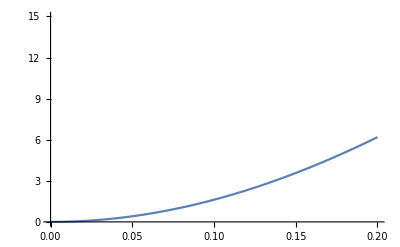

```mathematica
Plot[(pe)*100,{p,0,.2},PlotRange->{0,20}]
```

```mathematica
AD=1-Exp[-2 Pi ξ̄ Subscript[Ω, o]/Subscript[Ω̄, d]]
```

1-Abs[(36-47 p^2 π^2-2 π √(-p^2 (-36+5 p^2 π^2)^2))/((4+p^2 π^2) (9+4 p^2 π^2))]^((2 π)/ArcTan[(2 π √(p^2 (-36+5 p^2 π^2)^2))/(36-47 p^2 π^2)])

```mathematica
ξ̄=-1/Subscript[Ω, o]Log[Abs[λ1]]
```

-Log[Abs[(36-47 p^2 π^2-2 π √(-p^2 (-36+5 p^2 π^2)^2))/((4+p^2 π^2) (9+4 p^2 π^2))]]/(2 p π)

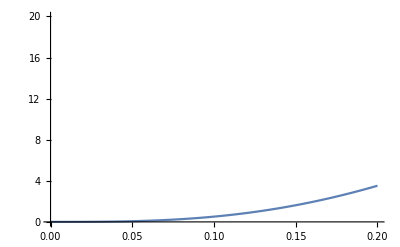

```mathematica
Plot[(AD)*100,{p,0,.2},PlotRange->{0,20}]
```

```mathematica
aNot=-({{Coefficient[Part[recursive,2],Subscript[ẋ, t]], Coefficient[Part[recursive,2],Subscript[x, t]]}, {Coefficient[Part[recursive,3],Subscript[ẋ, t]], Coefficient[Part[recursive,3],Subscript[x, t]]}})
```

{{144/((9+(4 π^2 Δt^2)/T^2) (16+(4 π^2 Δt^2)/T^2))-(188 π^2 Δt^2)/(T^2 (9+(4 π^2 Δt^2)/T^2) (16+(4 π^2 Δt^2)/T^2)),-(384 π^2 Δt)/(T^2 (9+(4 π^2 Δt^2)/T^2) (16+(4 π^2 Δt^2)/T^2))+(16 π^4 Δt^3)/(T^4 (9+(4 π^2 Δt^2)/T^2) (16+(4 π^2 Δt^2)/T^2))},{(144 Δt)/((9+(4 π^2 Δt^2)/T^2) (16+(4 π^2 Δt^2)/T^2))-(20 π^2 Δt^3)/(T^2 (9+(4 π^2 Δt^2)/T^2) (16+(4 π^2 Δt^2)/T^2)),144/((9+(4 π^2 Δt^2)/T^2) (16+(4 π^2 Δt^2)/T^2))-(76 π^2 Δt^2)/(T^2 (9+(4 π^2 Δt^2)/T^2) (16+(4 π^2 Δt^2)/T^2))}}

```mathematica
eigaNot=Eigenvalues[aNot]/.Δt->p T//Expand//Simplify//Cancel;
```

```mathematica
ppp={0,Part[eigaNot,1],Part[eigaNot,2]}
```

{0,(36 T^4-33 p^2 π^2 T^4-2 π √(-p^2 (864-205 p^2 π^2+5 p^4 π^4) T^8))/((4+p^2 π^2) (9+4 p^2 π^2) T^4),(36 T^4-33 p^2 π^2 T^4+2 π √(-p^2 (864-205 p^2 π^2+5 p^4 π^4) T^8))/((4+p^2 π^2) (9+4 p^2 π^2) T^4)}

```mathematica
qqq=eigA
```

{0,(36 T^4-47 p^2 π^2 T^4-2 π √(-p^2 (-36+5 p^2 π^2)^2 T^8))/((4+p^2 π^2) (9+4 p^2 π^2) T^4),(36 T^4-47 p^2 π^2 T^4+2 π √(-p^2 (-36+5 p^2 π^2)^2 T^8))/((4+p^2 π^2) (9+4 p^2 π^2) T^4)}

```mathematica
ppp-qqq//Simplify
```

{0,(2 π (7 p^2 π T^4+√(-p^2 (-36+5 p^2 π^2)^2 T^8)-√(-p^2 (864-205 p^2 π^2+5 p^4 π^4) T^8)))/((4+p^2 π^2) (9+4 p^2 π^2) T^4),(2 π (7 p^2 π T^4-√(-p^2 (-36+5 p^2 π^2)^2 T^8)+√(-p^2 (864-205 p^2 π^2+5 p^4 π^4) T^8)))/((4+p^2 π^2) (9+4 p^2 π^2) T^4)}